```mathematica
Needs["PlotLegends`"]
```

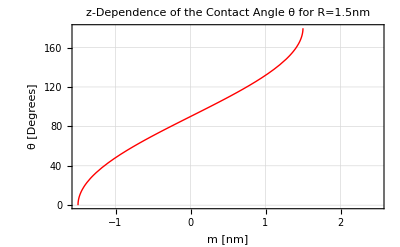

```mathematica
R= 1.5;
pl15=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=1.5nm", PlotStyle->{Red, Thick}]
```

2.

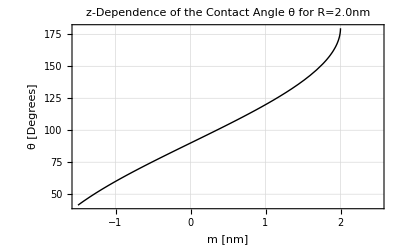

```mathematica
R = 2.0
pl20=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=2.0nm",PlotStyle->{Black,Thick}]
```

2.5

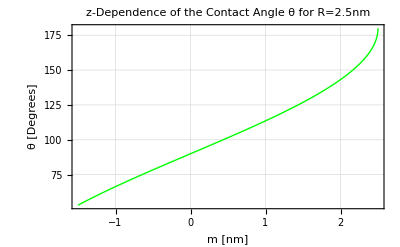

```mathematica
R = 2.5
pl25=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=2.5nm",PlotStyle->{Green,Thick}]
```

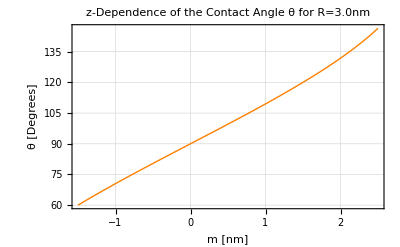

```mathematica
R = 3.0;
pl30=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=3.0nm", PlotStyle->{Orange, Thick}]
```

3.5

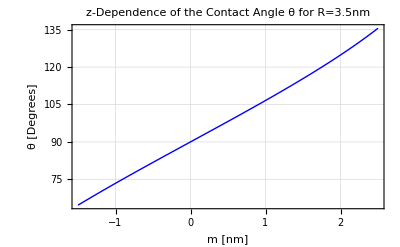

```mathematica
R = 3.5
pl35=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=3.5nm",PlotStyle->{Blue,Thick}]
```

1.

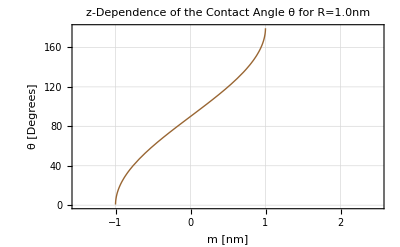

```mathematica
R = 1.0
pl10=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=1.0nm",PlotStyle->{Brown,Thick}]
```

Graphics::gprim: Null was encountered where a Graphics primitive or directive was expected.

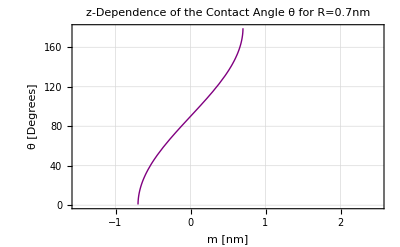

```mathematica
R = 0.7;
pl07=Plot[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)*(180/Pi),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=0.7nm",PlotStyle->{Purple,,Thick}]
```

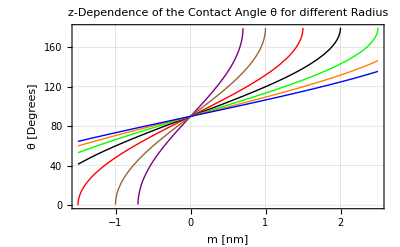

```mathematica
Show[{pl07,pl10,pl15, pl20, pl25, pl30, pl35},PlotLabel->"z-Dependence of the Contact Angle θ for different Radius"]
```

```mathematica
Show[{pl07,pl10,pl15, pl20, pl25, pl30, pl35},PlotLabel->"z-Dependence of the Contact Angle θ for different Radius"] LineLegend[{Directive[Purple,Thick],Directive[ Brown,Thick],Directive[Red,Thick],Directive[Black,Thick],Directive[ Green,Thick],Directive[Orange,Thick],Directive[Blue,Thick]},{"R = 0.7 nm","R = 1.0 nm","R = 1.5 nm","R = 2.0 nm","R = 2.5 nm","R = 3.0 nm","R = 3.5 nm"},LegendFunction->"Frame",LabelStyle->20]
```

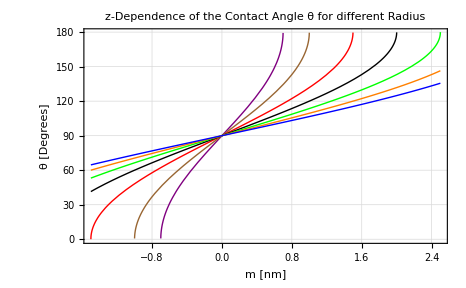
```mathematica
-Graphics- -Graphics-
```

-1.5

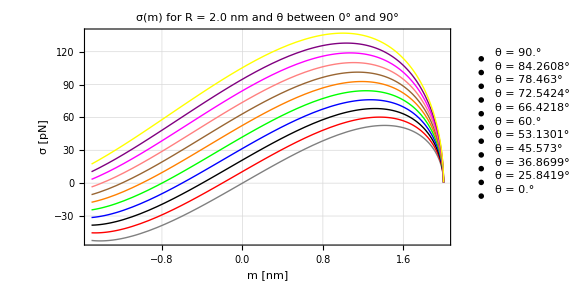

```mathematica
R = 2.0;
costheta=0.1;
m =0.0;
deltaM=2.5;
deltamin =-1.5
theta01=ArcCos[costheta]*(180/Pi);
σl1501=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Red, Thick}];
costheta=0.2;
theta02=ArcCos[costheta]*(180/Pi);
σl1502=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Black, Thick}];
costheta=0.3;
theta03=ArcCos[costheta]*(180/Pi);
σl1503=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Blue, Thick}];
costheta=0.4;
theta04=ArcCos[costheta]*(180/Pi);
σl1504=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Green, Thick}];
costheta=0.5;
theta05=ArcCos[costheta]*(180/Pi);
σl1505=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Orange, Thick}];
costheta=0.6;
theta06=ArcCos[costheta]*(180/Pi);
σl1506=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Brown, Thick}];
costheta=0.7;
theta07=ArcCos[costheta]*(180/Pi);
σl1507=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Pink, Thick}];
costheta=0.8;
theta08=ArcCos[costheta]*(180/Pi);
σl1508=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Magenta, Thick}];
costheta=0.9;
theta09=ArcCos[costheta]*(180/Pi);
σl1509=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"},PlotStyle->{Purple, Thick}];
costheta=1.0;
theta10=ArcCos[costheta]*(180/Pi);
σl1510=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Yellow, Thick}];
costheta=0.0;
theta00=ArcCos[costheta]*(180/Pi);
σl1500=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Gray, Thick}];
ShowLegend[Show[{σl1500,σl1501,σl1502,σl1503,σl1504,σl1505,σl1506,σl1507,σl1508,σl1509,σl1510},ImageSize->Large,PlotRange->All,PlotLabel->"σ(m) for R = 2.0 nm and θ between 0° and 90° "],{{{Graphics@{Thick,Gray,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta00]<>"°"},{Graphics@{Thick,Red,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta01]<>"°"},{Graphics@{Thick,Black,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta02]<>"°"},{Graphics@{Thick,Blue,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta03]<>"°"},{Graphics@{Thick,Green,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta04]<>"°"},{Graphics@{Thick,Orange,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta05]<>"°"},{Graphics@{Thick,Brown,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta06]<>"°"},{Graphics@{Thick,Pink,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta07]<>"°"},{Graphics@{Thick,Magenta,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta08]<>"°"},{Graphics@{Thick,Purple,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta09]<>"°"},{Graphics@{Thick,Yellow,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta10]<>"°"}},LegendPosition->{1,-0.3}, LegendTextSpace->6, LegendTextOffset->Automatic}]
```

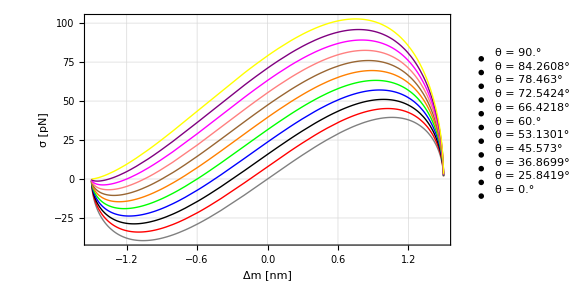

-1.5

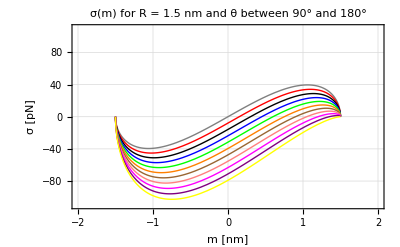

```mathematica
R = 1.5;
costheta=-0.1;
m =0.0;
deltaM=2.5;
deltamin =-1.5
mintheta01=ArcCos[costheta]*(180/Pi);
minσl1501=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Red, Thick}];
costheta=-0.2;
mintheta02=ArcCos[costheta]*(180/Pi);
minσl1502=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Black, Thick}];
costheta=-0.3;
mintheta03=ArcCos[costheta]*(180/Pi);
minσl1503=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Blue, Thick}];
costheta=-0.4;
mintheta04=ArcCos[costheta]*(180/Pi);
minσl1504=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Green, Thick}];
costheta=-0.5;
mintheta05=ArcCos[costheta]*(180/Pi);
minσl1505=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Orange, Thick}];
costheta=-0.6;
mintheta06=ArcCos[costheta]*(180/Pi);
minσl1506=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Brown, Thick}];
costheta=-0.7;
mintheta07=ArcCos[costheta]*(180/Pi);
minσl1507=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Pink, Thick}];
costheta=-0.8;
mintheta08=ArcCos[costheta]*(180/Pi);
minσl1508=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Magenta, Thick}];
costheta=-0.9;
mintheta09=ArcCos[costheta]*(180/Pi);
minσl1509=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"},PlotStyle->{Purple, Thick}];
costheta=-1.0;
mintheta10=ArcCos[costheta]*(180/Pi);
minσl1510=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Yellow, Thick}];
costheta=0.0;
mintheta00=ArcCos[costheta]*(180/Pi);
minσl1500=Plot[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-costheta)*Sqrt[R^2 - (m )^2]*(-52.7),{m,deltamin, deltaM}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","σ [pN]"}, PlotStyle->{Gray, Thick}];
Show[minσl1500,minσl1501,minσl1502,minσl1503,minσl1504,minσl1505,minσl1506,minσl1507,minσl1508,minσl1509,minσl1510,PlotRange->{{-2,2},{-110,110}},PlotLabel->"σ(m) for R = 1.5 nm and θ between 90° and 180° "]
LineLegend[{Directive[Red,Thick],Directive[ Black,Thick],Directive[Blue,Thick],Directive[Green,Thick],Directive[ Orange,Thick],Directive[Brown,Thick],Directive[Pink,Thick],Directive[Magenta,Thick],Directive[Purple,Thick],Directive[Yellow,Thick],Directive[Gray,Thick]},{"θ = "<>ToString[mintheta01]<>"°","θ = "<>ToString[mintheta02]<>"°","θ = "<>ToString[mintheta03]<>"°","θ = "<>ToString[mintheta04]<>"°","θ = "<>ToString[mintheta05]<>"°","θ = "<>ToString[mintheta06]<>"°","θ = "<>ToString[mintheta07]<>"°","θ = "<>ToString[mintheta08]<>"°","θ = "<>ToString[mintheta09]<>"°","θ = "<>ToString[mintheta10]<>"°","θ = "<>ToString[mintheta00]<>"°"},LegendFunction->"Frame",LabelStyle->20]
```

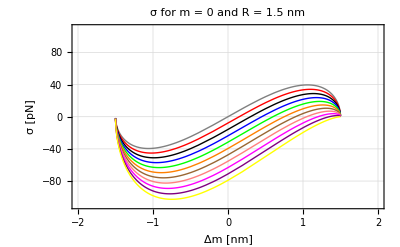

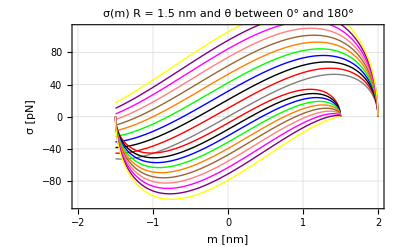

```mathematica
Show[σl1500,σl1501,σl1502,σl1503,σl1504,σl1505,σl1506,σl1507,σl1508,σl1509,σl1510,minσl1501,minσl1502,minσl1503,minσl1504,minσl1505,minσl1506,minσl1507,minσl1508,minσl1509,minσl1510,PlotRange->{{-2,2},{-110,110}},PlotLabel->"σ(m) R = 1.5 nm and θ between 0° and 180° "]
```

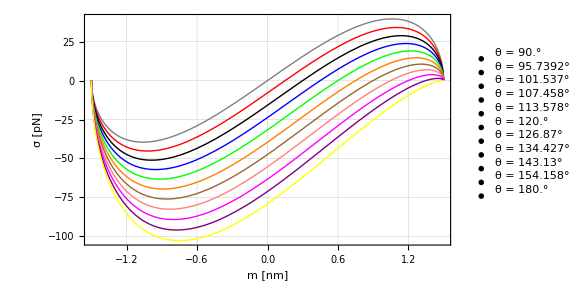

```mathematica
ShowLegend[Show[{minσl1500,minσl1501,minσl1502,minσl1503,minσl1504,minσl1505,minσl1506,minσl1507,minσl1508,minσl1509,minσl1510},ImageSize->Large,PlotRange->All],{{{Graphics@{Thick,Gray,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta00]<>"°"},{Graphics@{Thick,Red,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta01]<>"°"},{Graphics@{Thick,Black,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta02]<>"°"},{Graphics@{Thick,Blue,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta03]<>"°"},{Graphics@{Thick,Green,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta04]<>"°"},{Graphics@{Thick,Orange,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta05]<>"°"},{Graphics@{Thick,Brown,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta06]<>"°"},{Graphics@{Thick,Pink,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta07]<>"°"},{Graphics@{Thick,Magenta,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta08]<>"°"},{Graphics@{Thick,Purple,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta09]<>"°"},{Graphics@{Thick,Yellow,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta10]<>"°"}},LegendPosition->{1,-0.3}, LegendTextSpace->6, LegendTextOffset->Automatic}]
```

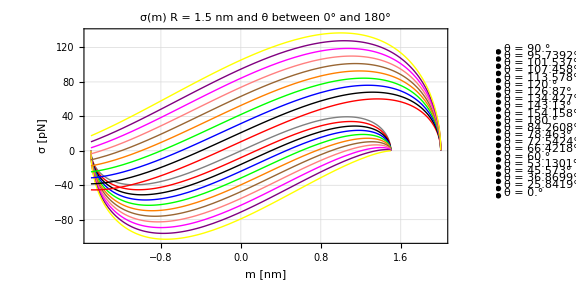

```mathematica
ShowLegend[Show[{minσl1500,minσl1501,minσl1502,minσl1503,minσl1504,minσl1505,minσl1506,minσl1507,minσl1508,minσl1509,minσl1510,σl1501,σl1502,σl1503,σl1504,σl1505,σl1506,σl1507,σl1508,σl1509,σl1510},ImageSize->Large,PlotRange->All,PlotLabel->"σ(m) R = 1.5 nm and θ between 0° and 180° "],{{{Graphics@{Thick,Gray,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta00]<>"°"},{Graphics@{Thick,Red,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta01]<>"°"},{Graphics@{Thick,Black,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta02]<>"°"},{Graphics@{Thick,Blue,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta03]<>"°"},{Graphics@{Thick,Green,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta04]<>"°"},{Graphics@{Thick,Orange,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta05]<>"°"},{Graphics@{Thick,Brown,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta06]<>"°"},{Graphics@{Thick,Pink,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta07]<>"°"},{Graphics@{Thick,Magenta,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta08]<>"°"},{Graphics@{Thick,Purple,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta09]<>"°"},{Graphics@{Thick,Yellow,Line[{{0,0},{1,0}}]},"θ = "<>ToString[mintheta10]<>"°"},{Graphics@{Thick,Red,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta01]<>"°"},{Graphics@{Thick,Black,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta02]<>"°"},{Graphics@{Thick,Blue,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta03]<>"°"},{Graphics@{Thick,Green,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta04]<>"°"},{Graphics@{Thick,Orange,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta05]<>"°"},{Graphics@{Thick,Brown,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta06]<>"°"},{Graphics@{Thick,Pink,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta07]<>"°"},{Graphics@{Thick,Magenta,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta08]<>"°"},{Graphics@{Thick,Purple,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta09]<>"°"},{Graphics@{Thick,Yellow,Line[{{0,0},{1,0}}]},"θ = "<>ToString[theta10]<>"°"}},LegendPosition->{1.1,-0.3}, LegendTextSpace->10, LegendTextOffset->Automatic}]
```

```mathematica
R=0.7;
p3d1=Plot3D[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-theta Degree)*Sqrt[R^2 - (m )^2]*(-52.7),{m,-1.5, 2.0}, {theta, 0,180},AxesLabel->{"m [nm]","θ [deg]","σ [pN]"},PlotLabel->"Line Tension σ(m, θ) for R = 0.7 nm",PlotStyle->Directive[Orange,Specularity[White,10]],FaceGrids->All,FaceGridsStyle->Directive[Orange,Dashed]]
```

-Graphics3D-

```mathematica
R=1.0;
p3d2=Plot3D[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-theta Degree)*Sqrt[R^2 - (m )^2]*(-52.7),{m,-1.5, 3}, {theta, 0,180},AxesLabel->{"m [nm]","θ [deg]","σ [pN]"},PlotLabel->"Line Tension σ(m, θ) for R = 1.0 nm",PlotStyle->Directive[Yellow,Specularity[White,20]],FaceGrids->All,FaceGridsStyle->Directive[Orange,Dashed]]
```

-Graphics3D-

```mathematica
R=1.5;
p3d3=Plot3D[(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-theta Degree)*Sqrt[R^2 - (m )^2]*(-52.7),{m,-1.5, 3}, {theta, 0,180},AxesLabel->{"m [nm]","θ [deg]","σ [pN]"},PlotLabel->"Line Tension σ(m, θ) for R = 1.5 nm",PlotStyle->Directive[Blue,Specularity[White,5]],FaceGrids->All,FaceGridsStyle->Directive[Orange,Dashed]]
```

-Graphics3D-

```mathematica
Show[{p3d1,p3d2, p3d3},PlotLabel->"Line Tension σ(m, θ) for R = 0.7, 1.0 and 1.5 nm"]
```

-Graphics3D-

```mathematica
R=1.5;
Solve[{x==(Cos[(ArcTan[(m)/Sqrt[R^2 - (m )^2]]+Pi/2)]-theta)*Sqrt[R^2 - (m )^2]*(-52.7),ArcSin[m/R]+ArcCos[m/R]==Pi/2},{x,m}]
```

Solve::ivar: 0. is not a valid variable.

Solve[{x==-79.05 (6.12323×10^-17-theta),True},{x,0.}]

```mathematica
Solve[ArcSin[x/R]+ArcCos[x/R]==Pi/2,x]
```

{{}}

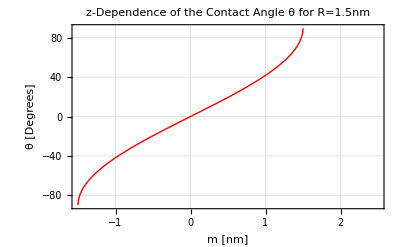

```mathematica
R= 1.5;
pl15=Plot[(ArcSin[(m/R)]/Degree),{m,-1.5, 2.5}, Frame->True,GridLines->Automatic, FrameLabel->{"m [nm]","θ [Degrees]"},PlotLabel->"z-Dependence of the Contact Angle θ for R=1.5nm", PlotStyle->{Red, Thick}]
```

```mathematica
R=1.5;
p3d3=Plot3D[Cos[(Sqrt[R^2 - (m )^2]/R)+Pi/2]-theta Degree*Sqrt[R^2 - (m )^2]*(-52.7),{m,-1.5, 3}, {theta, 0,180},AxesLabel->{"m [nm]","θ [deg]","σ [pN]"},PlotLabel->"Line Tension σ(m, θ) for R = 1.5 nm",PlotStyle->Directive[Blue,Specularity[White,5]],FaceGrids->All,FaceGridsStyle->Directive[Orange,Dashed]]
```